## 第5章 数值计算方法

联机帮助：Numerical Operations on Functions

### 5.1 插值

```mathematica
data=Table[{x,Sin[x]},{x,-π,π,0.2π}];ListPlot[data]
```

例：多项式插值

```mathematica
Clear[f,x];f=InterpolatingPolynomial[data,x]
Plot[f,{x,-π,π}]
```

例：样条函数

```mathematica
Clear[f,x];f=Interpolation[data]
Plot[f[x],{x,-Pi,Pi}]
```

### 5.2 曲线拟合

例：线性拟合

```mathematica
Clear[f,x];f=Fit[data,{1,x,x^2,x^3},x]
Plot[f,{x,-Pi,Pi}]
```

例：参数拟合

```mathematica
Clear[a,b,c,f,x];sol=FindFit[data,a Cos[b x+c],{a,b,c},x]
f=a Cos[b x+c]/.sol
Plot[f,{x,-Pi,Pi}]
```

### 5.3 数值积分

```mathematica
NIntegrate[ √(1-x^2),{x,0,1}]-π/4
```

例：求圆柱体{y^2+z^2≤1
-1≤x≤1 与平面 z=a x+b y+c 相交的截面面积。

```mathematica
Clear[f];f[a_,b_,c_]:=NIntegrate[Boole[y^2+(a x+b y+c)^2≤1],{x,-1,1},{y,-1,1}];
```

```mathematica
Plot[f[0.3,0.4,c],{c,-2,2}]
```

### 5.4 非线性方程求根

例：非线性方程

```mathematica
Plot[{0.1x,Cos[x]},{x,-10,10}]
```

```mathematica
NSolve[Cos[x]==0.1x,x,Reals]
```

```mathematica
FindRoot[Cos[x]==0.1x,{x,0}]
```

例：非线性方程组

```mathematica
Show[ContourPlot[x^3+y^3==1+x+y,{x,-2,2},{y,-2,2}],ContourPlot[x^2+y^2==2,{x,-2,2},{y,-2,2}]]
```

```mathematica
NSolve[{x^3+y^3==1+x+y,x^2+y^2==2},{x,y}]
```

```mathematica
FindRoot[{x^3+y^3==1+x+y,x^2+y^2==2},{{x,0},{y,1}}]
```

### 5.5 函数极值

例：一元函数的极值或最值

```mathematica
Clear[f,x];f=Exp[-x^2] Sin[6 x];Plot[f,{x,-2,2},PlotRange->All]
```

```mathematica
FindMinimum[f,{x,1}]
```

```mathematica
FindMinimum[{f,1≤x≤2},{x,1.5}]
```

```mathematica
NMinimize[f,x]
```

```mathematica
NMinimize[{f,1≤x≤2},x]
```

例：求点使得到定点的距离之和最小

```mathematica
Clear[a,f,x];a=RandomReal[{-1,1},{3,2}]
f=Sum[Norm[{x,y}-a⟦i⟧],{i,3}];
Show[ContourPlot[f,{x,-1,1},{y,-1,1}],ListPlot[a,PlotStyle->Red]]
```

```mathematica
sol=FindMinimum[f,{x,0},{y,0}]
```

```mathematica
NMinimize[f,{x,y}]
```

```mathematica
NMinimize[{f,x^2+y^2==1},{x,y}]
```

例：线性规划 Minimize_(A x≥ b, x≥0) c^T x
求 f(x,y,z)=4x+5y+3z 在约束条件Piecewise[{{4x+3y+6z≤120, □}, {2x+4y+5z≤100, □}, {x,y,z≥0, □}}] 下的最小值。

```mathematica
Clear[a,b,c,x];a=({{4, 3, 6}, {2, 4, 5}});b={120,100};c={4,5,3};
x=LinearProgramming[-c,-a,-b]
c.x
```

### 5.6 微分方程数值解

例：常微分方程

```mathematica
Clear[x,y];DSolve[{y'[x]==x^2-y[x]^3,y[0]==1},y[x],x]
```

```mathematica
sol=NDSolve[{y'[x]==x^2-y[x]^3,y[0]==1},y[x],{x,0,5}]
```

```mathematica
Plot[y[x]/.sol⟦1⟧,{x,0,5}]
```

```mathematica
Clear[x,y,t];DSolve[{x'[t]==x[t]-x[t]*y[t],y'[t]==-y[t]+x[t]*y[t]},{x[t],y[t]},t]
```

```mathematica
sol=NDSolve[{x'[t]==x[t]-x[t]*y[t],y'[t]==-y[t]+x[t]y[t],x[0]==0.1,y[0]==0.5},{x[t],y[t]},{t,0,10}]
```

```mathematica
ParametricPlot[{x[t],y[t]}/.sol⟦1⟧,{t,0,10}]
```

例：偏微分方程

```mathematica
Clear[u,t,x];DSolve[{D[u[t,x],t]==D[u[t,x],{x,2}],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u[t,x],{t,x}]
```

```mathematica
sol=NDSolve[{D[u[t,x],t]==D[u[t,x],{x,2}],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0.1t},u[t,x],{t,0,10},{x,0,5}]
```

```mathematica
Plot3D[u[t,x]/.sol⟦1⟧,{t,0,10},{x,0,5},AxesLabel->{t,x},PlotRange->All]
```

### 5.7 概率统计

联机帮助：Probability & Statistics

例：随机数和随机变量的生成

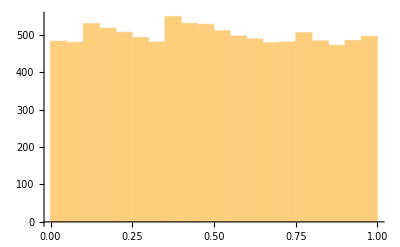

```mathematica
x=RandomReal[{0,1},10^4];Histogram[x]
```

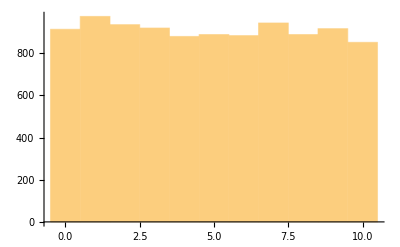

```mathematica
x=RandomInteger[{0,10},10^4];Histogram[x]
```

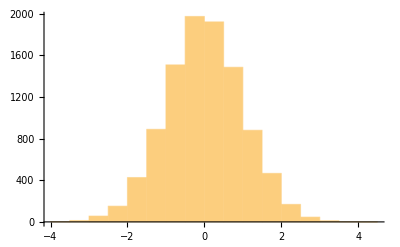

```mathematica
x=RandomReal[NormalDistribution[0,1],10^4];Histogram[x]
```

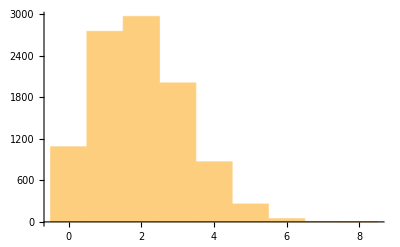

```mathematica
x=RandomInteger[BinomialDistribution[10,0.2],10^4];Histogram[x]
```

例：参数估计

```mathematica
Clear[n,p];NSolve[{n*p==Mean[x],n*p*(1-p)==Variance[x]},{n,p}]
```

{{n→9.89307,p→0.200362}}

例：在单位球面 S^2 上随机选取一点

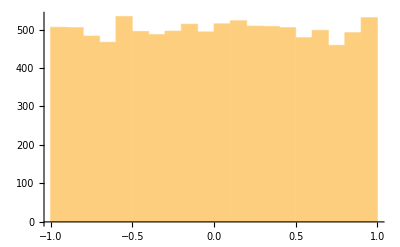

```mathematica
x=Table[Normalize[RandomReal[NormalDistribution[],3]],10^4];Histogram[x⟦All,1⟧]
```

例：随机生成一个3阶正交方阵

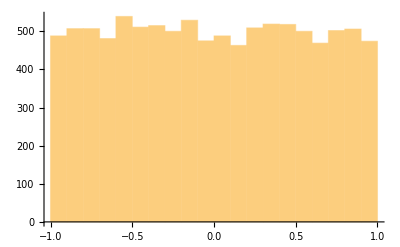

```mathematica
x=Table[Orthogonalize[RandomReal[NormalDistribution[],{3,3}]],10^4];Histogram[x⟦All,1,1⟧]
```

例：模拟Poisson过程

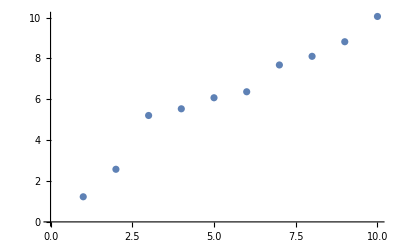

```mathematica
λ=2;n=10;(* x⟦k⟧是第k个事件发生的时刻 *)
x=Accumulate[RandomReal[ExponentialDistribution[1/λ],n]];ListPlot[x]
```

例：模拟随机过程X_n=a X_(n-1)+b X_(n-2)+N(0,σ^2)

```mathematica
{a,b}=RandomReal[{-0.5,0.5},2];σ=RandomReal[];{a,b,σ}
```

{0.150083,-0.0608884,0.201611}

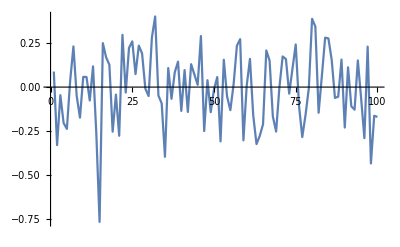

```mathematica
n=100;x=RandomReal[NormalDistribution[0,σ],n];x⟦2⟧+=a x⟦1⟧;
Do[x⟦i⟧+=a x⟦i-1⟧+b x⟦i-2⟧,{i,3,n}];ListLinePlot[x]
```

例：回归分析

```mathematica
test[data_,p_]:=Module[{a,b,n,x},
n=Length[data];a=Table[data⟦i+j-1⟧,{i,n-p},{j,p}];b=data⟦p+1;;n⟧;x=LeastSquares[a,b];Prepend[x,Norm[a.x-b]/(√(n-p))]
];
Table[test[x,p],{p,5}]//TableForm
```

0.207692 | 0.0653268 |  |  |  | 
0.204955 | -0.0981102 | 0.0780901 |  |  | 
0.205625 | -0.0617664 | -0.0947058 | 0.0699526 |  | 
0.205328 | 0.0151718 | -0.0569694 | -0.111547 | 0.0700098 | 
0.202124 | 0.163654 | 0.00655492 | -0.0563747 | -0.102096 | 0.0555754